```mathematica
(*with rfd, 5000 non interacting particles*)
SetDirectory[NotebookDirectory[]];
dir="/home/drladiges/gigan/projects/FHDeX/exec/";
(*dir="/home/drladiges/kumongaRoot/scratch/drladiges/results_DISCOS2/WCA_ES_fullwet/";*)
file="ascii_means000075000";
count=2;
(*slist={"A","C"};*)
slist={"E","F"};(*eo wet 0*)
(*slist={"E","F","G","H"};*)(*eo damp 0*)
(*slist={"I","J","K","L"};*)(*eo wet 120*)
rawList=Table[0,{ii,1,count}];
(*dir="/home/drladiges/projects/FHDeX/exec/";.
file="ascii_means000000150";*)

For[kk=1,kk≤count,kk++,
raw0=Import[dir<>"immersedIons"<>slist[[kk]]<>"/0_"<>file,"Table"];
raw1=Import[dir<>"immersedIons"<>slist[[kk]]<>"/1_"<>file,"Table"];
raw2=Import[dir<>"immersedIons"<>slist[[kk]]<>"/2_"<>file,"Table"];
raw3=Import[dir<>"immersedIons"<>slist[[kk]]<>"/3_"<>file,"Table"];
raw4=Import[dir<>"immersedIons"<>slist[[kk]]<>"/4_"<>file,"Table"];
raw5=Import[dir<>"immersedIons"<>slist[[kk]]<>"/5_"<>file,"Table"];
raw6=Import[dir<>"immersedIons"<>slist[[kk]]<>"/6_"<>file,"Table"];
raw7=Import[dir<>"immersedIons"<>slist[[kk]]<>"/7_"<>file,"Table"];
rawA=Join[raw0[[1;;-3]],raw1[[1;;-3]],raw2[[1;;-3]],raw3[[1;;-3]],raw4[[1;;-3]],raw5[[1;;-3]],raw6[[1;;-3]],raw7[[1;;-3]]];
rawList[[kk]]=rawA;
];
```

```mathematica
(*xsize=64;
ysize=64;
zsize=32;*)
xsize=128;
ysize=128;
zsize=64;
cell=1;

func3D=Table[0,{ii,1,count}];
func2D=Table[0,{ii,1,count}];

For[ll=1,ll≤count,ll++,
members3DA=Table[{ToExpression[StringReplace[rawList[[ll,ii,1]],{"("-> "{",")"-> "}"}]],rawList[[ll,ii,3]]},{ii,1,Length[rawList[[ll]]]}];
func3D[[ll]]=Interpolation[members3DA,InterpolationOrder->1];
membersFlat=Flatten[Table[{{ii,jj},Mean[Table[func3D[[ll]][ii,jj,kk],{kk,0,zsize-1,cell}]]},{ii,0,xsize-1},{jj,0,ysize-1}],1];
func2D[[ll]]=Interpolation[membersFlat,InterpolationOrder->1];
];
```

```mathematica
func3D1=Table[0,{ii,1,count}];
func2D1=Table[0,{ii,1,count}];

For[ll=1,ll≤count,ll++,
members3DA1=Table[{ToExpression[StringReplace[rawList[[ll,ii,1]],{"("-> "{",")"-> "}"}]],rawList[[ll,ii,-3]]},{ii,1,Length[rawList[[ll]]]}];
func3D1[[ll]]=Interpolation[members3DA1,InterpolationOrder->1];
membersFlat1=Flatten[Table[{{ii,jj},Mean[Table[func3D1[[ll]][ii,jj,kk],{kk,0,zsize-1,cell}]]},{ii,0,xsize-1},{jj,0,ysize-1}],1];
func2D1[[ll]]=Interpolation[membersFlat1,InterpolationOrder->1];
];
```

```mathematica
func3D2=Table[0,{ii,1,count}];
func2D2=Table[0,{ii,1,count}];

For[ll=1,ll≤count,ll++,
members3DA2=Table[{ToExpression[StringReplace[rawList[[ll,ii,1]],{"("-> "{",")"-> "}"}]],rawList[[ll,ii,-2]]},{ii,1,Length[rawList[[ll]]]}];
func3D2[[ll]]=Interpolation[members3DA2,InterpolationOrder->1];
membersFlat2=Flatten[Table[{{ii,jj},Mean[Table[func3D2[[ll]][ii,jj,kk],{kk,0,zsize-1,cell}]]},{ii,0,xsize-1},{jj,0,ysize-1}],1];
func2D2[[ll]]=Interpolation[membersFlat2,InterpolationOrder->1];
];
```

```mathematica
func2DM[x_,y_] = Sum[func2D[[ll]][x,y],{ll,1,count}]/count;
func2DM1[x_,y_] = Sum[func2D1[[ll]][x,y],{ll,1,count}]/count;
func2DM2[x_,y_] = Sum[func2D2[[ll]][x,y],{ll,1,count}]/count;
```

```mathematica
DensityPlot[func2DM[x,y],{x,0,xsize-1},{y,0,ysize-1},ColorFunction->"SunsetColors",PlotLegends->Automatic,PlotPoints->256]
DensityPlot[func2DM1[x,y],{x,0,xsize-1},{y,0,ysize-1},ColorFunction->"SunsetColors",PlotLegends->Automatic,PlotPoints->256]
DensityPlot[func2DM2[x,y],{x,0,xsize-1},{y,0,ysize-1},ColorFunction->"SunsetColors",PlotLegends->Automatic,PlotPoints->256]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
membersFlatter=Flatten[Table[{{jj,Mean[Table[func2DM[ii,jj],{ii,0,xsize-1,cell}]]}},{jj,0,ysize-1}],1];
func1DM=Interpolation[membersFlatter,InterpolationOrder->1];

membersFlatter1=Flatten[Table[{{jj,Mean[Table[func2DM1[ii,jj],{ii,0,xsize-1,cell}]]}},{jj,0,ysize-1}],1];
func1DM1=Interpolation[membersFlatter1,InterpolationOrder->1];

membersFlatter2=Flatten[Table[{{jj,Mean[Table[func2DM2[ii,jj],{ii,0,xsize-1,cell}]]}},{jj,0,ysize-1}],1];
func1DM2=Interpolation[membersFlatter2,InterpolationOrder->1];
```

```mathematica
size=13.06*10^-7;
dx=size/xsize;
posFunc[x_]=x/dx -0.5;

m1=Graphics[{Thick,Red,Circle[{0,0},1]}];
m2=Graphics[{Thick,Black,Line[{{-0.5,-0.5},{0.5,-0.5},{0.5,0.5},{-0.5,0.5},{-0.5,-0.5}}]}];
m3=Graphics[{Thick,Purple,Line[{{-0.5,-0.5},{0.5,0.5}}],Line[{{-0.5,0.5},{0.5,-0.5}}]}];
m4=Graphics[{Thick,Green,Line[{{0,-0.5},{-0.5,0},{0,0.5},{0.5,0},{0,-0.5}}]}];

ml1=Graphics[Line[{{0.25size,-20},{0.25size,900}}]];
ml2=Graphics[Line[{{0.75size,-20},{0.75size,900}}]];
```

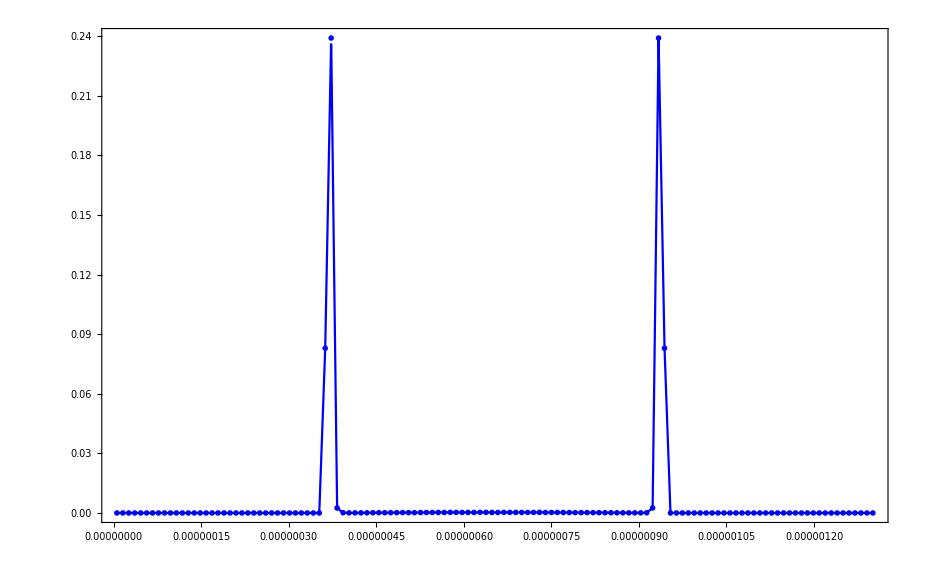

```mathematica
pa=ListPlot[Table[{y,(func1DM1[posFunc[y]]+func1DM1[posFunc[size-y]])/2},{y,dx/2,size-dx/2,dx}],PlotStyle->Blue,PlotMarkers->{m2,0.03}];
pb=Plot[(func1DM1[posFunc[y]]+func1DM1[posFunc[size-y]])/2,{y,dx/2,size-dx/2},PlotRange->All,PlotStyle->Blue];
pc=ListPlot[Table[{y,(func1DM2[posFunc[y]]+func1DM2[posFunc[size-y]])/2},{y,dx/2,size-dx/2,dx}],PlotStyle->Blue,PlotMarkers->{m2,0.03}];
pd=Plot[(func1DM2[posFunc[y]]+func1DM2[posFunc[size-y]])/2,{y,dx/2,size-dx/2},PlotRange->All,PlotStyle->Blue];
Show[pa,pb,PlotRange->All,Frame->True,Axes->False]
```

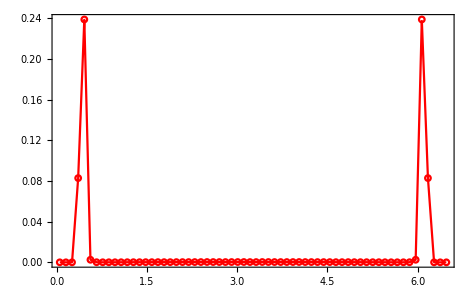

```mathematica
pa=ListPlot[Table[{y,(func1DM1[posFunc[size-(y+0.25size)]]+func1DM1[posFunc[(y+0.25size)]])/2},{y,dx/2,0.5size-dx/2,dx}],PlotMarkers->{m1,0.03},PlotRange->{0,900}];
pb=Plot[(func1DM1[posFunc[size-(y+0.25size)]]+func1DM1[posFunc[y+0.25size]])/2,{y,dx/2,0.5size-dx/2},PlotStyle->Red,PlotRange->{0,900}];
Show[pa,pb,Frame->True,Axes->False,AxesOrigin->{0,0},PlotRange->All]
```

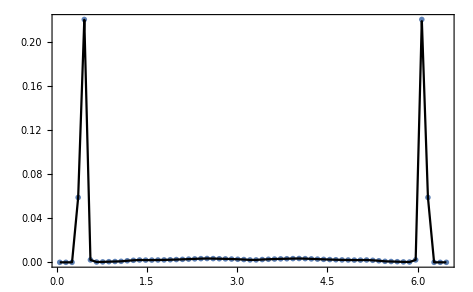
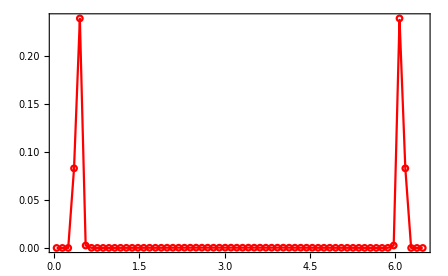
```mathematica
dist50=-Graphics-;
dist100=-Graphics-;
```

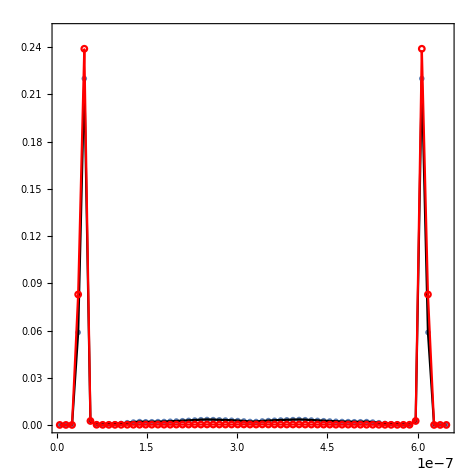

```mathematica
Show[dist50,dist100,AspectRatio->1, PlotRange->{0,0.25}]
```